Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Sampling Functions

```mathematica
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
zsample[l_]:= (Sign[Thread[l - RandomReal[1, Length[l]]]]+1)/2;
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
HiddenProbabilities[w_][v_]:=Logistic[wᵀ.v];
VisibleProbabilities[w_][h_]:= Most[Logistic[w.h]];
```

## Learning

```mathematica
DeltaWeight[ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew,v3,h3},
wnew=w;
Do[
h1=SampleHidden[w][v1];
v2=SampleVisible[w][h1];
h2=SampleHidden[w][v2];
v3=SampleVisible[w][h2];
h3=SampleHidden[w][v3];
(*
w0=1-Outer[BitXor, v1, h1];
w1=1-Outer[BitXor, v1, h3];*)
w0=Outer[Times, v1, h1];
w1=Outer[Times, v1, h3];

wnew += ϵ*(w0-w1);
,
{16}];
wnew
]
```

```mathematica
DataLearning[w_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n]
```

```mathematica
StepLearning[w_,ϵ_,n_,dataV_]:=Module[{w1,w2,w3},w1=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n/3];
w2=Nest[Function[DeltaWeight[ϵ/10,RandomChoice[dataV]][#]],w1,n/3];
w3=Nest[Function[DeltaWeight[ϵ/100,RandomChoice[dataV]][#]],w2,n/3];
w3
]
```

```mathematica
rot[s_,x_,y_,rx_,ry_]:=Module[ {x1=x,y1=y,tp},

If[ry==0,If[rx==1,x1=s-1-x;y1=s-1-y;];tp=x1;x1=y1;y1=tp;];
{s,x1,y1,rx,ry}
];
d2xy[n_][d_]:=Module[{rx,ry,t=d,x=0,y=0,s},
For[s=1,s<n,s*=2,rx=BitAnd[1,Floor[(t/2)]];ry=BitAnd[1,BitXor[t,rx]];
{s,x,y,rx,ry}=rot[s,x,y,rx,ry];x=x+(s*rx);y=y+(s*ry);t=Floor[t/4];
];
{x,y}
];
xy2d[n_][{x_,y_}]:=Module[{s,x1=x,y1=y,rx,ry,d=0},

For[s=Floor[n/2],s≥1,s=Floor[s/2],
If[BitAnd[x1,s]>0,rx=1,rx=0];
If[BitAnd[y1,s]>0,ry=1,ry=0];
d+=((s*s)*BitXor[(3*rx),ry]);
{s,x1,y1,rx,ry}=rot[s,x1,y1,rx,ry];
];
d
]
```

## Testing

```mathematica
N1=8;
SeedRandom[5];
Hn=1;Vn=((2*N1)+1);
W=RandomReal[{-0.5,0.5},{Vn,Hn}];
dataV=Append[#*2-1,1]& /@ {IntegerDigits[(2^N1)-1,2,2*N1],IntegerDigits[(2^(2*N1)-(2^N1)),2,2*N1]};
w1=StepLearning[W,0.02,6000,dataV];
```

```mathematica
probs={#,HiddenProbabilities[w1][Append[#,1]]}& /@Tuples[{-1,1},2*N1];
```

```mathematica
target=dataV[[1, ;;-2]];
distances={HammingDistance[#1,target],#2}& @@@ probs;
sets=GatherBy[distances,First];
hammingplot={#[[1,1]], Mean[#[[All,2,1]]]}& /@ sets;
```

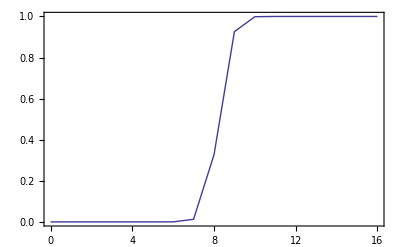

```mathematica
ListPlot[Sort[hammingplot],PlotRange->{All,{0,1}},PlotRangePadding->0.1,Frame->True,Joined->True]
```

```mathematica
kmap[n_]:=Module[{g,i,j,l={}},
g=graycode[n/2];
For[i=1,i≤2^(n/2),i++,
For[j=1,j≤2^(n/2),j++,AppendTo[l,Join[g[[i]],g[[j]]]] ]
];
l



]
```

```mathematica
k8=kmap[8];
```

```mathematica
kmaplist1=IntegerDigits[#,2,4]&/@{0,4,12,8,1,5,13,9,3,7,15,11,2,6,14,10}
```

{{0,0,0,0},{0,1,0,0},{1,1,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,1},{1,1,0,1},{1,0,0,1},{0,0,1,1},{0,1,1,1},{1,1,1,1},{1,0,1,1},{0,0,1,0},{0,1,1,0},{1,1,1,0},{1,0,1,0}}

```mathematica
kmaplist88=Flatten[HiddenProbabilities[w1][Append[#,1]]& /@(2*k8-1)];
```

```mathematica
euclidlist8=Table[euclid[i],{i,0,255}];
```

```mathematica
kmaplist8=Transpose[{kmaplist88,euclidlist8}];
```

```mathematica
graycode[n_]:=Map[IntegerDigits[#,2,n]&,Map[BitXor[#,Floor[#/2]]&,Range[0,2^n-1]]];
graylist = (2*graycode[2*N1]-1);
MapIndexed[Set[graydictionary[#1],First[#2]]&, graylist];
graycodeprobs={graydictionary[#1], #2}& @@@ probs;
```

```mathematica
arr=Array[0,{2^N1,2^N1}];
setarr[{p1_,p2_},col_]:=arr[[1+p1,1+p2]]=col;
setarr @@@ graycodeprobs;
ArrayPlot[arr,ImageSize->100]
```

-Graphics-

```mathematica
graym2=Flatten[HiddenProbabilities[w1][Append[#,1]]& /@(2*breckett8-1)];
```

{1.,1.,0.999993,0.994363,0.516984,0.00672398,6.73834×10^-6,4.10413×10^-8,3.59279×10^-11,5.89885×10^-9,5.63992×10^-6,0.00125135,1.31043×10^-6,0.00100227,4.51618×10^-6,0.000743813,9.72257×10^-7,0.0001537,0.133774,0.000975794,0.527357,0.0011094,6.76445×10^-6,5.9217×10^-9,5.66177×10^-6,0.000928723,0.171162,0.000215941,0.141897,0.963161,0.0330222,0.00020715,0.172288,0.000936096,9.32666×10^-7,0.00106427,6.48899×10^-6,0.00616598,0.0000392385,0.0291662,0.0000262987,0.004316,4.53367×10^-6,0.00100615,1.31551×10^-6,0.00131984,5.94901×10^-6,0.000939719,9.36279×10^-7,0.00106839,0.149372,0.994079,0.128143,0.991191,0.105299,0.000713546,0.13691,0.993764,0.417708,0.00435015,4.34906×10^-6,2.75067×10^-8,0.0000314205,0.00513248,0.831438,0.0064014,0.515007,0.995779,0.197901,0.0014947,0.600615,0.995812,0.191384,0.00143947,9.11728×10^-6,7.98143×10^-9,6.11059×10^-6,0.0058085,0.489599,0.00429942,0.415784,0.998603,0.812661,0.998544,0.472532,0.999024,0.866174,0.00563407,5.92605×10^-6,3.60938×10^-8,8.01821×10^-6,0.00131475,0.178297,0.994016,0.999962,0.971677,0.999974,0.975006,0.999973,0.9956,0.579528,0.0012051,0.480181,0.998924,0.547946,0.995,0.99997,0.970283,0.165345,0.000890938,0.504618,0.998719,0.405723,0.00414098,5.43122×10^-6,3.43511×10^-8,0.0000345085,0.00565577,0.482904,0.995203,0.999996,0.995982,0.999995,0.998831,0.427853,0.991613,0.418649,0.00453398,0.0000276329,0.0257407,0.854427,0.00610139,0.50197,0.00451656,0.83826,0.998781,0.449243,0.992617,0.999992,0.998771,0.831979,0.999092,0.869689,0.999088,0.588687,0.999305,0.999996,1.,0.999994,0.999063,0.866622,0.00674986,0.838784,0.00515226,0.459549,0.994734,0.999967,0.994512,0.999994,1.,0.999995,0.999132,0.534031,0.00693193,0.534993,0.00150048,0.589623,0.00642604,0.505585,0.000894386,0.473496,0.993273,0.999991,1.,0.999994,1.,0.999999,0.999799,0.967929,0.0379261,0.0000412291,0.00647677,5.70676×10^-6,5.68056×10^-9,1.26194×10^-6,0.000207952,0.137368,0.000716309,0.406655,0.998724,0.999999,1.,0.999999,0.999798,0.999999,0.999851,0.999999,0.999136,0.502936,0.993788,0.999993,0.993475,0.165879,0.00125619,7.63106×10^-6,0.00864187,0.897514,0.00760803,0.557268,0.998963,0.999993,0.99345,0.99996,1.,0.999994,0.993715,0.490565,0.998967,0.813249,0.99855,0.806853,0.00542671,0.861742,0.999278,0.999996,0.999028,0.51795,0.998786,0.999995,0.994533,0.4502,0.00494349,0.826087,0.99979,0.833083,0.0306006,0.875196,0.00907632,0.601542,0.999308,0.558222,0.99502,0.17284,0.00126616,0.492544,0.000965219,0.524637,0.999053,0.999994,0.995617,0.191983,0.995828,0.591537,0.999099,0.999999,1.}

```mathematica
euclid[n_]:={Quotient[n,16]+1,Mod[n ,16]+1};
```

```mathematica
t2=Transpose[{graym2,j1}]
```

{{1.,{1,1}},{1.,{1,2}},{0.999993,{1,3}},{0.994363,{1,4}},{0.516984,{1,5}},{0.00672398,{1,6}},{6.73834×10^-6,{1,7}},{4.10413×10^-8,{1,8}},{3.59279×10^-11,{1,9}},{5.89885×10^-9,{1,10}},{5.63992×10^-6,{1,11}},{0.00125135,{1,12}},{1.31043×10^-6,{1,13}},{0.00100227,{1,14}},{4.51618×10^-6,{1,15}},{0.000743813,{1,16}},{9.72257×10^-7,{2,1}},{0.0001537,{2,2}},{0.133774,{2,3}},{0.000975794,{2,4}},{0.527357,{2,5}},{0.0011094,{2,6}},{6.76445×10^-6,{2,7}},{5.9217×10^-9,{2,8}},{5.66177×10^-6,{2,9}},{0.000928723,{2,10}},{0.171162,{2,11}},{0.000215941,{2,12}},{0.141897,{2,13}},{0.963161,{2,14}},{0.0330222,{2,15}},{0.00020715,{2,16}},{0.172288,{3,1}},{0.000936096,{3,2}},{9.32666×10^-7,{3,3}},{0.00106427,{3,4}},{6.48899×10^-6,{3,5}},{0.00616598,{3,6}},{0.0000392385,{3,7}},{0.0291662,{3,8}},{0.0000262987,{3,9}},{0.004316,{3,10}},{4.53367×10^-6,{3,11}},{0.00100615,{3,12}},{1.31551×10^-6,{3,13}},{0.00131984,{3,14}},{5.94901×10^-6,{3,15}},{0.000939719,{3,16}},{9.36279×10^-7,{4,1}},{0.00106839,{4,2}},{0.149372,{4,3}},{0.994079,{4,4}},{0.128143,{4,5}},{0.991191,{4,6}},{0.105299,{4,7}},{0.000713546,{4,8}},{0.13691,{4,9}},{0.993764,{4,10}},{0.417708,{4,11}},{0.00435015,{4,12}},{4.34906×10^-6,{4,13}},{2.75067×10^-8,{4,14}},{0.0000314205,{4,15}},{0.00513248,{4,16}},{0.831438,{5,1}},{0.0064014,{5,2}},{0.515007,{5,3}},{0.995779,{5,4}},{0.197901,{5,5}},{0.0014947,{5,6}},{0.600615,{5,7}},{0.995812,{5,8}},{0.191384,{5,9}},{0.00143947,{5,10}},{9.11728×10^-6,{5,11}},{7.98143×10^-9,{5,12}},{6.11059×10^-6,{5,13}},{0.0058085,{5,14}},{0.489599,{5,15}},{0.00429942,{5,16}},{0.415784,{6,1}},{0.998603,{6,2}},{0.812661,{6,3}},{0.998544,{6,4}},{0.472532,{6,5}},{0.999024,{6,6}},{0.866174,{6,7}},{0.00563407,{6,8}},{5.92605×10^-6,{6,9}},{3.60938×10^-8,{6,10}},{8.01821×10^-6,{6,11}},{0.00131475,{6,12}},{0.178297,{6,13}},{0.994016,{6,14}},{0.999962,{6,15}},{0.971677,{6,16}},{0.999974,{7,1}},{0.975006,{7,2}},{0.999973,{7,3}},{0.9956,{7,4}},{0.579528,{7,5}},{0.0012051,{7,6}},{0.480181,{7,7}},{0.998924,{7,8}},{0.547946,{7,9}},{0.995,{7,10}},{0.99997,{7,11}},{0.970283,{7,12}},{0.165345,{7,13}},{0.000890938,{7,14}},{0.504618,{7,15}},{0.998719,{7,16}},{0.405723,{8,1}},{0.00414098,{8,2}},{5.43122×10^-6,{8,3}},{3.43511×10^-8,{8,4}},{0.0000345085,{8,5}},{0.00565577,{8,6}},{0.482904,{8,7}},{0.995203,{8,8}},{0.999996,{8,9}},{0.995982,{8,10}},{0.999995,{8,11}},{0.998831,{8,12}},{0.427853,{8,13}},{0.991613,{8,14}},{0.418649,{8,15}},{0.00453398,{8,16}},{0.0000276329,{9,1}},{0.0257407,{9,2}},{0.854427,{9,3}},{0.00610139,{9,4}},{0.50197,{9,5}},{0.00451656,{9,6}},{0.83826,{9,7}},{0.998781,{9,8}},{0.449243,{9,9}},{0.992617,{9,10}},{0.999992,{9,11}},{0.998771,{9,12}},{0.831979,{9,13}},{0.999092,{9,14}},{0.869689,{9,15}},{0.999088,{9,16}},{0.588687,{10,1}},{0.999305,{10,2}},{0.999996,{10,3}},{1.,{10,4}},{0.999994,{10,5}},{0.999063,{10,6}},{0.866622,{10,7}},{0.00674986,{10,8}},{0.838784,{10,9}},{0.00515226,{10,10}},{0.459549,{10,11}},{0.994734,{10,12}},{0.999967,{10,13}},{0.994512,{10,14}},{0.999994,{10,15}},{1.,{10,16}},{0.999995,{11,1}},{0.999132,{11,2}},{0.534031,{11,3}},{0.00693193,{11,4}},{0.534993,{11,5}},{0.00150048,{11,6}},{0.589623,{11,7}},{0.00642604,{11,8}},{0.505585,{11,9}},{0.000894386,{11,10}},{0.473496,{11,11}},{0.993273,{11,12}},{0.999991,{11,13}},{1.,{11,14}},{0.999994,{11,15}},{1.,{11,16}},{0.999999,{12,1}},{0.999799,{12,2}},{0.967929,{12,3}},{0.0379261,{12,4}},{0.0000412291,{12,5}},{0.00647677,{12,6}},{5.70676×10^-6,{12,7}},{5.68056×10^-9,{12,8}},{1.26194×10^-6,{12,9}},{0.000207952,{12,10}},{0.137368,{12,11}},{0.000716309,{12,12}},{0.406655,{12,13}},{0.998724,{12,14}},{0.999999,{12,15}},{1.,{12,16}},{0.999999,{13,1}},{0.999798,{13,2}},{0.999999,{13,3}},{0.999851,{13,4}},{0.999999,{13,5}},{0.999136,{13,6}},{0.502936,{13,7}},{0.993788,{13,8}},{0.999993,{13,9}},{0.993475,{13,10}},{0.165879,{13,11}},{0.00125619,{13,12}},{7.63106×10^-6,{13,13}},{0.00864187,{13,14}},{0.897514,{13,15}},{0.00760803,{13,16}},{0.557268,{14,1}},{0.998963,{14,2}},{0.999993,{14,3}},{0.99345,{14,4}},{0.99996,{14,5}},{1.,{14,6}},{0.999994,{14,7}},{0.993715,{14,8}},{0.490565,{14,9}},{0.998967,{14,10}},{0.813249,{14,11}},{0.99855,{14,12}},{0.806853,{14,13}},{0.00542671,{14,14}},{0.861742,{14,15}},{0.999278,{14,16}},{0.999996,{15,1}},{0.999028,{15,2}},{0.51795,{15,3}},{0.998786,{15,4}},{0.999995,{15,5}},{0.994533,{15,6}},{0.4502,{15,7}},{0.00494349,{15,8}},{0.826087,{15,9}},{0.99979,{15,10}},{0.833083,{15,11}},{0.0306006,{15,12}},{0.875196,{15,13}},{0.00907632,{15,14}},{0.601542,{15,15}},{0.999308,{15,16}},{0.558222,{16,1}},{0.99502,{16,2}},{0.17284,{16,3}},{0.00126616,{16,4}},{0.492544,{16,5}},{0.000965219,{16,6}},{0.524637,{16,7}},{0.999053,{16,8}},{0.999994,{16,9}},{0.995617,{16,10}},{0.191983,{16,11}},{0.995828,{16,12}},{0.591537,{16,13}},{0.999099,{16,14}},{0.999999,{16,15}},{1.,{16,16}}}

```mathematica
j1=Table[euclid[i],{i,0,255}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,15},{11,16},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,15},{13,16},{14,1},{14,2},{14,3},{14,4},{14,5},{14,6},{14,7},{14,8},{14,9},{14,10},{14,11},{14,12},{14,13},{14,14},{14,15},{14,16},{15,1},{15,2},{15,3},{15,4},{15,5},{15,6},{15,7},{15,8},{15,9},{15,10},{15,11},{15,12},{15,13},{15,14},{15,15},{15,16},{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16}}

```mathematica
euclidlist={#[[1]],euclid[#[[2]]]}&/@t1
```

```mathematica
hilbert=Transpose[{Table[i,{i,1,(2^(2*N1))}],Flatten[graym2]}];
MapHilbert[l_]:={#[[2]],d2xy[2^N1][#[[1]]]}&/@l;
h=MapHilbert[hilbert];
```

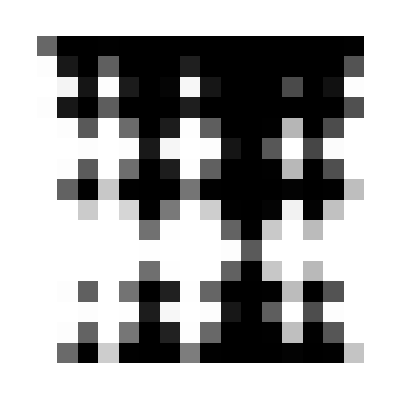

```mathematica
arr=Array[0,{2^N1,2^N1}];
setarr[col_, {p1_,p2_}]:=arr[[p1,p2]]=col;
setarr @@@ kmaplist8;
ArrayPlot[arr]
```

```mathematica
t2
```

{{1.,{1,1}},{1.,{1,2}},{0.999993,{1,3}},{0.994363,{1,4}},{0.516984,{1,5}},{0.00672398,{1,6}},{6.73834×10^-6,{1,7}},{4.10413×10^-8,{1,8}},{3.59279×10^-11,{1,9}},{5.89885×10^-9,{1,10}},{5.63992×10^-6,{1,11}},{0.00125135,{1,12}},{1.31043×10^-6,{1,13}},{0.00100227,{1,14}},{4.51618×10^-6,{1,15}},{0.000743813,{2,0}},{9.72257×10^-7,{2,1}},{0.0001537,{2,2}},{0.133774,{2,3}},{0.000975794,{2,4}},{0.527357,{2,5}},{0.0011094,{2,6}},{6.76445×10^-6,{2,7}},{5.9217×10^-9,{2,8}},{5.66177×10^-6,{2,9}},{0.000928723,{2,10}},{0.171162,{2,11}},{0.000215941,{2,12}},{0.141897,{2,13}},{0.963161,{2,14}},{0.0330222,{2,15}},{0.00020715,{3,0}},{0.172288,{3,1}},{0.000936096,{3,2}},{9.32666×10^-7,{3,3}},{0.00106427,{3,4}},{6.48899×10^-6,{3,5}},{0.00616598,{3,6}},{0.0000392385,{3,7}},{0.0291662,{3,8}},{0.0000262987,{3,9}},{0.004316,{3,10}},{4.53367×10^-6,{3,11}},{0.00100615,{3,12}},{1.31551×10^-6,{3,13}},{0.00131984,{3,14}},{5.94901×10^-6,{3,15}},{0.000939719,{4,0}},{9.36279×10^-7,{4,1}},{0.00106839,{4,2}},{0.149372,{4,3}},{0.994079,{4,4}},{0.128143,{4,5}},{0.991191,{4,6}},{0.105299,{4,7}},{0.000713546,{4,8}},{0.13691,{4,9}},{0.993764,{4,10}},{0.417708,{4,11}},{0.00435015,{4,12}},{4.34906×10^-6,{4,13}},{2.75067×10^-8,{4,14}},{0.0000314205,{4,15}},{0.00513248,{5,0}},{0.831438,{5,1}},{0.0064014,{5,2}},{0.515007,{5,3}},{0.995779,{5,4}},{0.197901,{5,5}},{0.0014947,{5,6}},{0.600615,{5,7}},{0.995812,{5,8}},{0.191384,{5,9}},{0.00143947,{5,10}},{9.11728×10^-6,{5,11}},{7.98143×10^-9,{5,12}},{6.11059×10^-6,{5,13}},{0.0058085,{5,14}},{0.489599,{5,15}},{0.00429942,{6,0}},{0.415784,{6,1}},{0.998603,{6,2}},{0.812661,{6,3}},{0.998544,{6,4}},{0.472532,{6,5}},{0.999024,{6,6}},{0.866174,{6,7}},{0.00563407,{6,8}},{5.92605×10^-6,{6,9}},{3.60938×10^-8,{6,10}},{8.01821×10^-6,{6,11}},{0.00131475,{6,12}},{0.178297,{6,13}},{0.994016,{6,14}},{0.999962,{6,15}},{0.971677,{7,0}},{0.999974,{7,1}},{0.975006,{7,2}},{0.999973,{7,3}},{0.9956,{7,4}},{0.579528,{7,5}},{0.0012051,{7,6}},{0.480181,{7,7}},{0.998924,{7,8}},{0.547946,{7,9}},{0.995,{7,10}},{0.99997,{7,11}},{0.970283,{7,12}},{0.165345,{7,13}},{0.000890938,{7,14}},{0.504618,{7,15}},{0.998719,{8,0}},{0.405723,{8,1}},{0.00414098,{8,2}},{5.43122×10^-6,{8,3}},{3.43511×10^-8,{8,4}},{0.0000345085,{8,5}},{0.00565577,{8,6}},{0.482904,{8,7}},{0.995203,{8,8}},{0.999996,{8,9}},{0.995982,{8,10}},{0.999995,{8,11}},{0.998831,{8,12}},{0.427853,{8,13}},{0.991613,{8,14}},{0.418649,{8,15}},{0.00453398,{9,0}},{0.0000276329,{9,1}},{0.0257407,{9,2}},{0.854427,{9,3}},{0.00610139,{9,4}},{0.50197,{9,5}},{0.00451656,{9,6}},{0.83826,{9,7}},{0.998781,{9,8}},{0.449243,{9,9}},{0.992617,{9,10}},{0.999992,{9,11}},{0.998771,{9,12}},{0.831979,{9,13}},{0.999092,{9,14}},{0.869689,{9,15}},{0.999088,{10,0}},{0.588687,{10,1}},{0.999305,{10,2}},{0.999996,{10,3}},{1.,{10,4}},{0.999994,{10,5}},{0.999063,{10,6}},{0.866622,{10,7}},{0.00674986,{10,8}},{0.838784,{10,9}},{0.00515226,{10,10}},{0.459549,{10,11}},{0.994734,{10,12}},{0.999967,{10,13}},{0.994512,{10,14}},{0.999994,{10,15}},{1.,{11,0}},{0.999995,{11,1}},{0.999132,{11,2}},{0.534031,{11,3}},{0.00693193,{11,4}},{0.534993,{11,5}},{0.00150048,{11,6}},{0.589623,{11,7}},{0.00642604,{11,8}},{0.505585,{11,9}},{0.000894386,{11,10}},{0.473496,{11,11}},{0.993273,{11,12}},{0.999991,{11,13}},{1.,{11,14}},{0.999994,{11,15}},{1.,{12,0}},{0.999999,{12,1}},{0.999799,{12,2}},{0.967929,{12,3}},{0.0379261,{12,4}},{0.0000412291,{12,5}},{0.00647677,{12,6}},{5.70676×10^-6,{12,7}},{5.68056×10^-9,{12,8}},{1.26194×10^-6,{12,9}},{0.000207952,{12,10}},{0.137368,{12,11}},{0.000716309,{12,12}},{0.406655,{12,13}},{0.998724,{12,14}},{0.999999,{12,15}},{1.,{13,0}},{0.999999,{13,1}},{0.999798,{13,2}},{0.999999,{13,3}},{0.999851,{13,4}},{0.999999,{13,5}},{0.999136,{13,6}},{0.502936,{13,7}},{0.993788,{13,8}},{0.999993,{13,9}},{0.993475,{13,10}},{0.165879,{13,11}},{0.00125619,{13,12}},{7.63106×10^-6,{13,13}},{0.00864187,{13,14}},{0.897514,{13,15}},{0.00760803,{14,0}},{0.557268,{14,1}},{0.998963,{14,2}},{0.999993,{14,3}},{0.99345,{14,4}},{0.99996,{14,5}},{1.,{14,6}},{0.999994,{14,7}},{0.993715,{14,8}},{0.490565,{14,9}},{0.998967,{14,10}},{0.813249,{14,11}},{0.99855,{14,12}},{0.806853,{14,13}},{0.00542671,{14,14}},{0.861742,{14,15}},{0.999278,{15,0}},{0.999996,{15,1}},{0.999028,{15,2}},{0.51795,{15,3}},{0.998786,{15,4}},{0.999995,{15,5}},{0.994533,{15,6}},{0.4502,{15,7}},{0.00494349,{15,8}},{0.826087,{15,9}},{0.99979,{15,10}},{0.833083,{15,11}},{0.0306006,{15,12}},{0.875196,{15,13}},{0.00907632,{15,14}},{0.601542,{15,15}},{0.999308,{16,0}},{0.558222,{16,1}},{0.99502,{16,2}},{0.17284,{16,3}},{0.00126616,{16,4}},{0.492544,{16,5}},{0.000965219,{16,6}},{0.524637,{16,7}},{0.999053,{16,8}},{0.999994,{16,9}},{0.995617,{16,10}},{0.191983,{16,11}},{0.995828,{16,12}},{0.591537,{16,13}},{0.999099,{16,14}},{0.999999,{16,15}},{1.,{16,16}}}